# gaussian smearing

## g switch, g smear, go futher with the transition probability

## the smearing function

```mathematica
f[x_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1}]
```

#### simplify the fourier transform

```mathematica
ftil[k]
```

(ⅇ^(-1/4 k^2 σ^2))/(√(1/σ^2) σ)

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0]
```

```mathematica
ftilGs[k_]:=ⅇ^(-1/4 k^2 σ^2)
```

## the transition probability

```mathematica
ggintegrandG[k_]:=-1/(2π)ⅇ^(-ε*k-1/2*η^2*(Ω+k)^2)*(-1+α*(2+ⅇ^(2*η^2*Ω*k)))*k*ftilGs[k]^2
```

### with an ε regularized cutoff (exp)

```mathematica
Integrate[ggintegrandG[k],{k,0,∞}]
```

ConditionalExpression[-1/(4 π (η^2+σ^2)^(3/2))ⅇ^(-1/2 η^2 Ω^2) ((α (√((η^2+σ^2) (ε-η^2 Ω)^2) (2 √(η^2+σ^2)+ⅇ^(((ε-η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (-ε+η^2 Ω))+ⅇ^(((ε-η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) √(η^2+σ^2) (ε-η^2 Ω)^2 Erf[(√((η^2+σ^2) (ε-η^2 Ω)^2))/(√2 (η^2+σ^2))]))/(√((η^2+σ^2) (ε-η^2 Ω)^2))+(√((η^2+σ^2) (ε+η^2 Ω)^2) (-2 √(η^2+σ^2)+ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (ε+η^2 Ω))-ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) √(η^2+σ^2) (ε+η^2 Ω)^2 Erf[(√((η^2+σ^2) (ε+η^2 Ω)^2))/(√2 (η^2+σ^2))])/(√((η^2+σ^2) (ε+η^2 Ω)^2))+(2 α (√((η^2+σ^2) (ε+η^2 Ω)^2) (2 √(η^2+σ^2)-ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (ε+η^2 Ω))+ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) √(η^2+σ^2) (ε+η^2 Ω)^2 Erf[(√((η^2+σ^2) (ε+η^2 Ω)^2))/(√2 (η^2+σ^2))]))/(√((η^2+σ^2) (ε+η^2 Ω)^2))),Re[η^2+σ^2]>0]

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε∈Reals&&ε>0&&Ω∈Reals]
```

-1/(4 π (η^2+σ^2)^(3/2))ⅇ^(-1/2 η^2 Ω^2) (1/Abs[ε-η^2 Ω]α ((2 √(η^2+σ^2)+ⅇ^(((ε-η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (-ε+η^2 Ω)) Abs[ε-η^2 Ω]+ⅇ^(((ε-η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (ε-η^2 Ω)^2 Erf[Abs[ε-η^2 Ω]/(√2 √(η^2+σ^2))])+1/Abs[ε+η^2 Ω]((-2 √(η^2+σ^2)+ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (ε+η^2 Ω)) Abs[ε+η^2 Ω]-ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (ε+η^2 Ω)^2 Erf[Abs[ε+η^2 Ω]/(√2 √(η^2+σ^2))])+1/Abs[ε+η^2 Ω]2 α ((2 √(η^2+σ^2)-ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (ε+η^2 Ω)) Abs[ε+η^2 Ω]+ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (ε+η^2 Ω)^2 Erf[Abs[ε+η^2 Ω]/(√2 √(η^2+σ^2))]))

```mathematica
FullSimplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε∈Reals&&ε>0&&Ω∈Reals]
```

```mathematica
pertexp[σ_,η_]:=1/(4 π (η^2+σ^2)^(3/2))ⅇ^(-1/2 η^2 Ω^2) (2 (1-3 α) √(η^2+σ^2)+√(2 π) (ⅇ^(((ε-η^2 Ω)^2)/(2 (η^2+σ^2))) α (ε-η^2 Ω) Erfc[(ε-η^2 Ω)/(√2 √(η^2+σ^2))]+ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) (-1+2 α) (ε+η^2 Ω) Erfc[(ε+η^2 Ω)/(√2 √(η^2+σ^2))]))
```

```mathematica
pexp[σ_,η_]:=α+λ^2*pertexp[σ,η]
```

### with no cutoff (ε:=0)

```mathematica
Simplify[pertexp[σ,η],Assumptions->ε==0]
```

```mathematica
pertnone[σ_,η_]:=1/(4 π (η^2+σ^2)^(3/2))ⅇ^(-1/2 η^2 Ω^2) (2 (1-3 α) √(η^2+σ^2)-ⅇ^((η^4 Ω^2)/(2 (η^2+σ^2))) √(2 π) α η^2 Ω Erfc[-(η^2 Ω)/(√2 √(η^2+σ^2))]+ⅇ^((η^4 Ω^2)/(2 (η^2+σ^2))) √(2 π) (-1+2 α) η^2 Ω Erfc[(η^2 Ω)/(√2 √(η^2+σ^2))])
```

```mathematica
pnone[σ_,η_]:=α+λ^2*pertnone[σ,η]
```

### with a sharp cutoff (ε:=0 and integrate only up to a constant)

```mathematica
Integrate[ggintegrandG[k],{k,0,5*Ω}]
```

-1/(2 π)(1/(2 (η^2+σ^2)^(3/2))(ⅇ^(-1/2 η^2 Ω ((2 ε)/(η^2+σ^2)+Ω)) α (2 ⅇ^((ε η^2 Ω)/(η^2+σ^2)) √(η^2+σ^2)+ⅇ^((ε^2+η^4 Ω^2)/(2 (η^2+σ^2))) √(2 π) (ε-η^2 Ω) Erf[(ε-η^2 Ω)/(√2 √(η^2+σ^2))])+ⅇ^(-1/2 η^2 Ω^2) (-1+2 α) (2 √(η^2+σ^2)+ⅇ^(((ε+η^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (ε+η^2 Ω) Erf[(ε+η^2 Ω)/(√2 √(η^2+σ^2))]))+1/(2 (η^2+σ^2)^(3/2))ⅇ^(-25/2 (η^2+σ^2) Ω^2) (ⅇ^(-5 ε Ω-1/2 η^2 Ω ((2 ε)/(η^2+σ^2)+Ω)) α (-2 ⅇ^(η^2 Ω (ε/(η^2+σ^2)+5 Ω)) √(η^2+σ^2)-ⅇ^(1/2 (10 ε Ω+25 (η^2+σ^2) Ω^2+(ε^2+η^4 Ω^2)/(η^2+σ^2))) √(2 π) (ε-η^2 Ω) Erf[(ε+4 η^2 Ω+5 σ^2 Ω)/(√2 √(η^2+σ^2))])-ⅇ^(-5 ε Ω-(11 η^2 Ω^2)/2) (-1+2 α) (2 √(η^2+σ^2)+ⅇ^(((ε+6 η^2 Ω+5 σ^2 Ω)^2)/(2 (η^2+σ^2))) √(2 π) (ε+η^2 Ω) Erf[(ε+6 η^2 Ω+5 σ^2 Ω)/(√2 √(η^2+σ^2))])))

```mathematica
Simplify[%,Assumptions->σ∈Reals&&σ>0&&η∈Reals&&η>0&&ε==0&&Ω∈Reals]
```

```mathematica
pertsharp[σ_,η_]:=1/(4 π (η^2+σ^2)^(3/2))ⅇ^(-1/2 (37 η^2+25 σ^2) Ω^2) (2 ⅇ^((21 η^2 Ω^2)/2) α √(η^2+σ^2)-2 ⅇ^(1/2 (36 η^2+25 σ^2) Ω^2) α √(η^2+σ^2)+2 ⅇ^((η^2 Ω^2)/2) (-1+2 α) √(η^2+σ^2)-2 ⅇ^(1/2 (36 η^2+25 σ^2) Ω^2) (-1+2 α) √(η^2+σ^2)-ⅇ^(((37 η^4+61 η^2 σ^2+25 σ^4) Ω^2)/(2 (η^2+σ^2))) √(2 π) (-1+2 α) η^2 Ω Erf[(η^2 Ω)/(√2 √(η^2+σ^2))]-ⅇ^(((37 η^4+61 η^2 σ^2+25 σ^4) Ω^2)/(2 (η^2+σ^2))) √(2 π) α η^2 Ω (Erf[(η^2 Ω)/(√2 √(η^2+σ^2))]+Erf[((4 η^2+5 σ^2) Ω)/(√2 √(η^2+σ^2))])+ⅇ^(((37 η^4+61 η^2 σ^2+25 σ^4) Ω^2)/(2 (η^2+σ^2))) √(2 π) (-1+2 α) η^2 Ω Erf[((6 η^2+5 σ^2) Ω)/(√2 √(η^2+σ^2))])
```

```mathematica
psharp[σ_,η_]:=α+λ^2*pertsharp[σ,η]
```

#### with a different cutoff (later) (ε:=0 and cutoff[k_]:=something)

## plot p v σ

#### assign the parameters numbers

```mathematica
η:=1
Ω:=1
α:=1
λ:=0.1
```

```mathematica
ε:=.25
```

#### clear the parameters of their numbers when necessary

```mathematica
Clear[σ];Clear[η];Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### plot p v σ

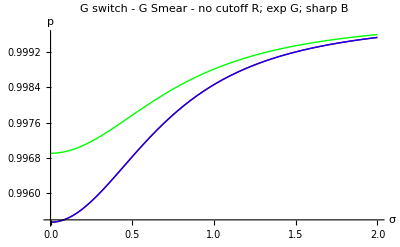

```mathematica
Plot[{pnone[σ,η],pexp[σ,η],psharp[σ,η]},{σ,0,2},
AxesLabel->{σ,p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["G switch - G Smear -\n no cutoff R; exp G; sharp B",FontSize->16]]
```

## plot p v σ for several values of η

#### parameterrrrrrs

```mathematica
Ω:=1
α:=1
λ:=0.1
ε:=0.25
η:={0.1,0.5,1.0,1.5}
```

#### cleeeaaaaar

```mathematica
Clear[σ];Clear[η];Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### plooooooooot PNONE

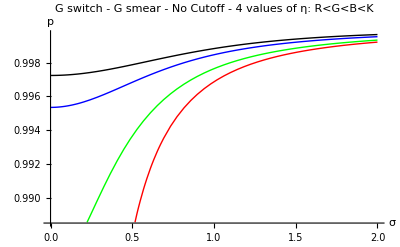

```mathematica
Plot[{pnone[σ,η[[1]]],pnone[σ,η[[2]]],pnone[σ,η[[3]]],pnone[σ,η[[4]]]},
{σ,0,2},
AxesLabel->{σ,p},
PlotStyle->{Red,Green,Blue,Black},
PlotRange->Automatic,
PlotLabel->Style["G switch - G smear - No Cutoff -\n 4 values of η: R<G<B<K",FontSize->16]]
```

#### plooooooooot PEXP

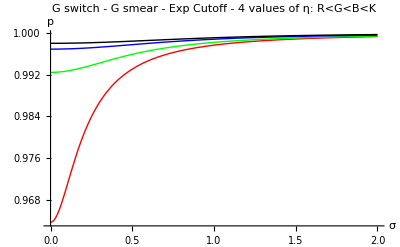

```mathematica
Plot[{pexp[σ,η[[1]]],pexp[σ,η[[2]]],pexp[σ,η[[3]]],pexp[σ,η[[4]]]},
{σ,0,2},
AxesLabel->{σ,p},
PlotStyle->{Red,Green,Blue,Black},
PlotRange->Full,
PlotLabel->Style["G switch - G smear - Exp Cutoff -\n 4 values of η: R<G<B<K",FontSize->16]]
```

#### plooooooooot PSHARP

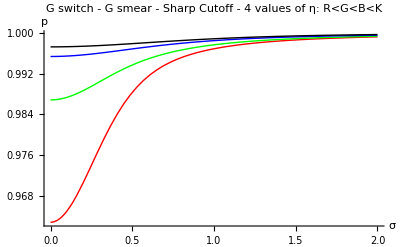

```mathematica
Plot[{psharp[σ,η[[1]]],psharp[σ,η[[2]]],psharp[σ,η[[3]]],psharp[σ,η[[4]]]},
{σ,0,2},
AxesLabel->{σ,p},
PlotStyle->{Red,Green,Blue,Black},
PlotRange->Full,
PlotLabel->Style["G switch - G smear - Sharp Cutoff -\n 4 values of η: R<G<B<K",FontSize->16]]
```

## plot p v η

#### assign the parameters numbers

```mathematica
σ:=.5
Ω:=1
α:=1
λ:=.1
```

```mathematica
ε:=0.25
```

#### clear parameters of numbers when necessary

```mathematica
Clear[σ];Clear[η];Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### plot p v η

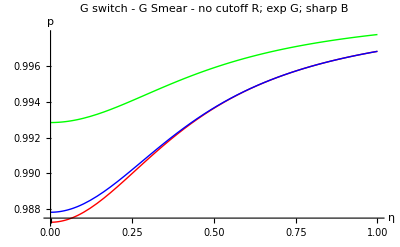

```mathematica
Plot[{pnone[σ,η],pexp[σ,η],psharp[σ,η]},{η,0,1},
AxesLabel->{η,p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["G switch - G Smear -\n no cutoff R; exp G; sharp B",FontSize->16]]
```

## plot p vs σ and η (!!!)

#### doo doo doo numbers

```mathematica
Ω:=1
α:=1
λ:=.1
ε:=0.25
```

#### doo doo doo clearing

```mathematica
Clear[σ];Clear[η];Clear[Ω];Clear[α];Clear[λ];Clear[ε];
```

#### contour plot of PNONE

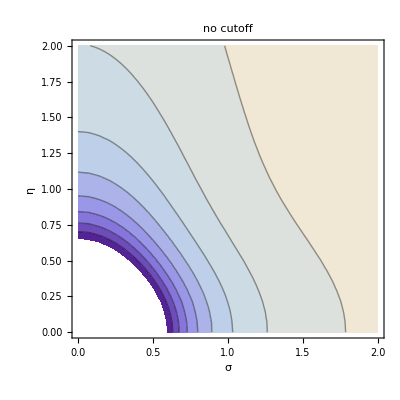

```mathematica
ContourPlot[pnone[σ,η],{σ,0,2},{η,0,2},
FrameLabel->Automatic,
PlotLabel->"no cutoff"]
```

#### contour plot of PEXP

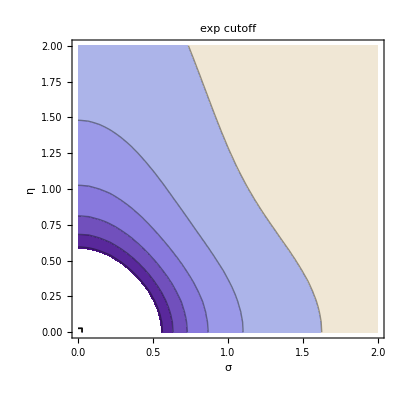

```mathematica
ContourPlot[pexp[σ,η],{σ,0,2},{η,0,2},
FrameLabel->Automatic,
PlotLabel->"exp cutoff"]
```

#### contour plot of PSHARP

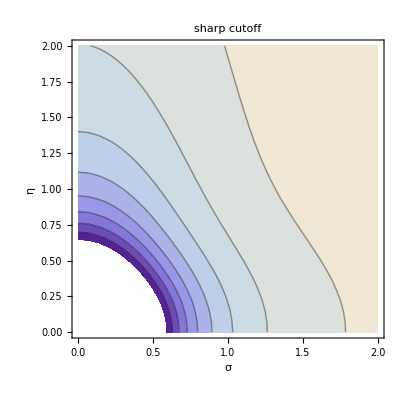

```mathematica
ContourPlot[psharp[σ,η],{σ,0,2},{η,0,2},
FrameLabel->Automatic,
PlotLabel->"sharp cutoff"]
```

#### contour plot of PNONE - PSHARP --- largest difference on the scale of 10^-4!!!

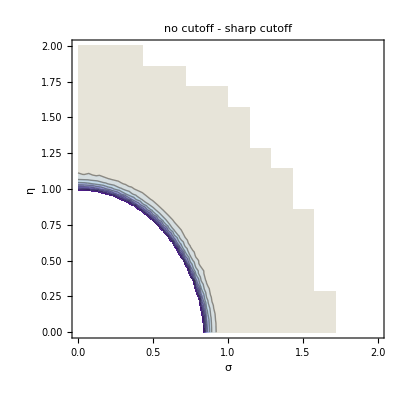

```mathematica
ContourPlot[pnone[σ,η]-psharp[σ,η],{σ,0,2},{η,0,2},
FrameLabel->Automatic,
PlotLabel->"no cutoff - sharp cutoff"]
```

## status

there is a maximum of p wrt both σ and η.